# Measure meeting angles & test generalized Gibbs–Thomson relation in the 3-species mutual detachment system

Import Comsol simulation of a triple interface junction on a circular domain in the 3-species McRD system with mutual detachment.

## Setup

### Load format specifiers to import Comsol data

```mathematica
NotebookEvaluate[NotebookDirectory[]<>"Comsol2Mathematica2hdf5.nb",
InsertResults->False,
EvaluationElements->Automatic
];
```

### Functions for fitting junctions

The interfaces are determined based on the squared norm of the gradient of the total-density fields B (m2+c2) & C (m3+c3).
These gradient fields are evaluated in Comsol and exported on a square grid.
We fit the interfaces by a combination of an arc (for the AB / AC interfaces) with constant curvature and a straight line for the BC interface (due to symmetry of the chosen parameters).
Fitting is done by determining the minimal distance of each point of the square grid to the interface line (arc + straight line; function “pointLoss” below). The loss function is defined as the sum over these distances squared weighted by the value of the squared norm of the gradient. The sum is performed for both the gradients of field B and C and runs in each case over all points on the grid for which the squared norm of the gradient is at least half the maximum value (function “lossCircleLine”). This latter condition excludes weak gradients occuring outside the fitted interface regions.
To account for the offset between the maxima of the gradients of field B and C in the BC interface, a shift dInt is included in the fitting.
To find the minimum of the loss function the Mathematica function FindMinimum is used (function “fitCircleLine”).

```mathematica
ClearAll@pointLoss;
pointLoss[pnt_,x0_,R_,phiInt_,phiLin_]:=Block[{
xint=x0+R{Cos[phiInt],Sin[phiInt]},
eLin={Cos[phiLin],Sin[phiLin]},
eLinN={-Sin[phiLin],Cos[phiLin]},
ePhi={-Sin[phiInt],Cos[phiInt]}*Sign[{Cos[phiLin],Sin[phiLin]}.{-Sin[phiInt],Cos[phiInt]}],
dx,dxLin,dxPhi
},
dx=pnt[[;;2]]-xint;
dxLin=dx.eLin;
dxPhi=dx.ePhi;
pnt[[3]]*
If[dxPhi>=0,
If[dxLin>=0,
(dx.eLinN)^2,
Norm[dx]^2
],
If[dxLin>=0,
Min[{(dx.eLinN)^2,(R-Norm[pnt[[;;2]]-x0])^2}],
(R-Norm[pnt[[;;2]]-x0])^2
]
]
];
```

```mathematica
ClearAll@lossCircleLine;
lossCircleLine[dataSelB_,dataSelC_,xJunc_?VectorQ,dInt_?NumericQ,R_?NumericQ,phiCircleB_?NumericQ,phiLin_?NumericQ]:=Block[{
lossB,
lossC,
x0,(*circle center*)
phiInt,(*angular direction from circle center to intersection point of circle (AB/AC interface) and line (BC interface)*)
eLinN={-Sin[phiLin],Cos[phiLin]}} (*normal vector of the BC interface (pointing in the direction at angle Pi/2+phiLin)*),
x0=xJunc+dInt*eLinN+R{Cos[phiCircleB],Sin[phiCircleB]};
phiInt=phiCircleB-Pi;
lossB=Mean[pointLoss[#,x0,R,phiInt,phiLin]&/@dataSelB];
x0=xJunc+ReflectionMatrix[eLinN].(dInt*eLinN+R{Cos[phiCircleB],Sin[phiCircleB]});
phiInt=-phiCircleB+2phiLin+Pi;
lossC=Mean[pointLoss[#,x0,R,phiInt,phiLin]&/@dataSelC];
lossB+lossC(*+1000Max[0,xJunc[[1]]-1000]^2 (*regularization to break degeneracy if junction point leaves the simulation domain at low meeting angles*)*)
];
```

```mathematica
ClearAll@fitCircleLine;
fitCircleLine[dataB_,dataC_,grid_,iniCond_]:=Block[{
xyDataB,
linDataB,
xyDataC,
linDataC,
max,
dataSelB,
dataSelC,
xJunc,(*coord. of junction point*)
x,(*x-coord. of junction*)
y,(*y-coord. of junction*)
dInt,(*normal offset from junction point of BC interface measured by B or C grad. *)
R,(*curvature radius of AB and AC interfaces*)
phiCircleB,(*angular direction from intersection point of circle and line to center of circle*)
phiLin,(*angular direction of line (BC interface)*)
fitRes
},
xyDataB=Transpose[{grid[[All,All,1]],grid[[All,All,2]],dataB},{3,1,2}];
(*xyDataB=Table[{indx,indy,dataB[[indy,indx]]},{indx,Length@dataB[[1]]},{indy,Length@dataB}];*)
linDataB=Flatten[xyDataB,1];
max=Max@linDataB[[All,3]];
dataSelB=Select[linDataB,#[[3]]>max/10&]; (*get rid of near-zero values; changed here compared to the case of mutually-suppressed attachment because gradients at AB & AC interfaces become weak*)

xyDataC=Transpose[{grid[[All,All,1]],grid[[All,All,2]],dataC},{3,1,2}];
(*xyDataC=Table[{indx,indy,dataC[[indy,indx]]},{indx,Length@dataC[[1]]},{indy,Length@dataC}];*)
linDataC=Flatten[xyDataC,1];
max=Max@linDataC[[All,3]];
dataSelC=Select[linDataC,#[[3]]>max/10&];

fitRes=Last@FindMinimum[
lossCircleLine[dataSelB,dataSelC,{x,y},dInt,100R,phiCircleB,phiLin],
{
{x,First[xJunc/.iniCond],Min[grid[[1]]],Max[grid[[1]]]},
{y,Last[xJunc/.iniCond],Min[grid[[1]]],Max[grid[[1]]]},
{dInt,dInt/.iniCond,-10,10},
{R,R/100/.iniCond,10^-2,10^2},
{phiCircleB,phiCircleB/.iniCond,0,2Pi},
{phiLin,phiLin/.iniCond,-Pi,Pi}
},AccuracyGoal->5,PrecisionGoal->5];

{
xJunc->({x,y}/.fitRes),
dInt->(dInt/.fitRes),
R->(100R/.fitRes),
phiCircleB->(phiCircleB/.fitRes),
phiLin->(phiLin/.fitRes)
}
];
```

### Functions for measuring the effective interfacial tensions

The effective interfacial tensions are calculated far from the junction from the cross section of the single interfaces.

```mathematica
ClearAll@evalPoints;(*adapt to the geometry of the interfaces (tangent vector of AC interface points towards/away from the junction if center of fitted circle lies right/left of interface)*)
evalPoints[angles_,domainRadius_]:=Quiet[{
{
(xJunc/.angles[[3]])+(domainRadius-xJunc[[1]])/2{Cos[phiLin],Sin[phiLin]},
{Cos[phiLin],Sin[phiLin]}
},
{
(xJunc/.angles[[3]])+dInt{-Sin[phiLin],Cos[phiLin]}+R{Cos[phiCircleB],Sin[phiCircleB]}-R{Cos[phiCircleB+(domainRadius)/2/R],Sin[phiCircleB+(domainRadius)/2/R]},
{-Sin[phiCircleB+(domainRadius)/2/R],Cos[phiCircleB+(domainRadius)/2/R]}
},
{
(xJunc/.angles[[3]])-dInt{-Sin[phiLin],Cos[phiLin]}+R{Cos[-phiCircleB+2phiLin],Sin[-phiCircleB+2phiLin]}-R{Cos[-phiCircleB+2phiLin-(domainRadius)/2/R],Sin[-phiCircleB+2phiLin-(domainRadius)/2/R]},
{-Sin[-phiCircleB+2phiLin-(domainRadius)/2/R],Cos[-phiCircleB+2phiLin-(domainRadius)/2/R]}
}
}/.angles[[3]]];
```

```mathematica
ClearAll@measureσ;
measureσ[angles_,dataσ_,grid_]:=Block[{
measurementPoints,
tvecBC,
nvecBC,
tvecAC,
nvecAC,
tvecAB,
nvecAB,
xyData,
dataAC,
dataAB,
dataBC,
σABAC,
σBC,
BCDomainCorners,
boundaryDist,
junctionDist,
dx=Abs[grid[[1,2,1]]-grid[[1,1,1]]],
L=Max[grid[[1,All,1]]]+Abs[grid[[1,2,1]]-grid[[1,1,1]]]/2
},
(*determine geometry of rectangles to measure σ*)
measurementPoints=evalPoints[angles,L];
tvecBC=measurementPoints[[1,2]];
nvecBC={-#[[2]],#[[1]]}&@measurementPoints[[1,2]];
tvecAC=measurementPoints[[2,2]];
nvecAC={#[[2]],-#[[1]]}&@measurementPoints[[2,2]];
tvecAB=measurementPoints[[3,2]];
nvecAB={#[[2]],-#[[1]]}&@measurementPoints[[3,2]];

xyData=Transpose[{grid[[All,All,1]],grid[[All,All,2]],dataσ},{3,1,2}];
dataAC={nvecAC.(#[[{1,2}]]-measurementPoints[[2,1]]),#[[3]]}&/@Select[Flatten[xyData[[Floor[Length[xyData]/2];;]](*These restrictions to certain parts of the data are to make the selection faster. Needs to be changed depending on where the junction is positioned within the data.*),1],((Abs[tvecAC.(#[[{1,2}]]-measurementPoints[[2,1]])]<2)&&(Abs[nvecAC.(#[[{1,2}]]-measurementPoints[[2,1]])]<1.5))&];

dataAB={nvecAB.(#[[{1,2}]]-measurementPoints[[3,1]]),#[[3]]}&/@Select[Flatten[xyData[[;;Floor[Length[xyData]/2]]],1],((Abs[tvecAB.(#[[{1,2}]]-measurementPoints[[3,1]])]<2)&&(Abs[nvecAB.(#[[{1,2}]]-measurementPoints[[3,1]])]<1.5))&];
(*determine σAB=σAC as average of the both measurements*)
σABAC=(Total[dataAC[[All,2]]]+Total[dataAB[[All,2]]])*dx^2/8;

BCDomainCorners={#+1.5nvecBC,#-1.5nvecBC}&@measurementPoints[[1,1]]+2tvecBC;
boundaryDist=dist/.FindRoot[Max[Norm/@(BCDomainCorners+dist tvecBC)]==L,{dist,0}];
(*ensure that the edge of the measurement region is at least 1 distant from the junction*)
junctionDist=Norm[measurementPoints[[1,1]]-(xJunc/.angles[[3]])]-2;
If[junctionDist>1,
dataBC={nvecBC.(#[[{1,2}]]-measurementPoints[[1,1]]),#[[3]]}&/@Select[Flatten[xyData[[All,Floor[Length[xyData[[1]]]/2];;]],1],((Abs[tvecBC.(#[[{1,2}]]-measurementPoints[[1,1]])]<2)&&(Abs[nvecBC.(#[[{1,2}]]-measurementPoints[[1,1]])]<1.5))&];
σBC=Total[dataBC[[All,2]]]*dx^2/4;,
If[boundaryDist>0,
dataBC={nvecBC.(#[[{1,2}]]-measurementPoints[[1,1]]),#[[3]]}&/@Select[Flatten[xyData[[All,Floor[Length[xyData[[1]]]/2];;]],1],(((tvecBC.(#[[{1,2}]]-measurementPoints[[1,1]]))<2)&&((tvecBC.(#[[{1,2}]]-measurementPoints[[1,1]]))>-(2+junctionDist-1))&&(Abs[nvecBC.(#[[{1,2}]]-measurementPoints[[1,1]])]<1.5))&];
σBC=Total[dataBC[[All,2]]]*dx^2/(4+junctionDist-1);,
dataBC={nvecBC.(#[[{1,2}]]-measurementPoints[[1,1]]),#[[3]]}&/@Select[Flatten[xyData[[All,Floor[Length[xyData[[1]]]/2];;]],1],(((tvecBC.(#[[{1,2}]]-measurementPoints[[1,1]]))<(2+boundaryDist))&&((tvecBC.(#[[{1,2}]]-measurementPoints[[1,1]]))>-(2+junctionDist-1))&&(Abs[nvecBC.(#[[{1,2}]]-measurementPoints[[1,1]])]<1.5))&];
σBC=Total[dataBC[[All,2]]]*dx^2/(4+junctionDist-1+boundaryDist);
]
];

Print[
ListPlot[{dataAC,dataBC},PlotRange->All]
];
{σABAC,σBC}
];
```

### Functions for measuring the core turnover

To calculate the core turnover, one first calculates the triangular area around the junction core in which the core turnover is calculated.
To this end, the function evalPointsCT uses the junction positions and interface directions fitted above. Assuming the specific layout of the interfaces, it calculates the intersection points of the triangle edges with the interfaces and the tangent vectors of the interfaces at these points.
The function measureCT calculates the core turnover from the modified core turnover by evaluating its integral over the triangular region.

```mathematica
ClearAll@evalPointsCT;
evalPointsCT[angles_]:=Quiet[{
{
(xJunc/.angles[[3]])+4{Cos[phiLin],Sin[phiLin]},
{Cos[phiLin],Sin[phiLin]}
},
{
(xJunc/.angles[[3]])+dInt{-Sin[phiLin],Cos[phiLin]}+R{Cos[phiCircleB],Sin[phiCircleB]}-R{Cos[phiCircleB+4/R],Sin[phiCircleB+4/R]},
{-Sin[phiCircleB+4/R],Cos[phiCircleB+4/R]}
},
{
(xJunc/.angles[[3]])-dInt{-Sin[phiLin],Cos[phiLin]}+R{Cos[-phiCircleB+2phiLin],Sin[-phiCircleB+2phiLin]}-R{Cos[-phiCircleB+2phiLin-4/R],Sin[-phiCircleB+2phiLin-4/R]},
{-Sin[-phiCircleB+2phiLin-4/R],Cos[-phiCircleB+2phiLin-4/R]}
}
}/.angles[[3]]];
```

```mathematica
ClearAll@measureCT;(*adapt signs of tangent vectors in the triangleTests to the geometry of the interfaces*)
measureCT[angles_,{dataCTx_,dataCTy_},gridCT_]:=Block[{
measurementPoints,
tvecBC,
tvecAC,
tvecAB,
xyData,
triangleTests,
coreData,
dataAC,
dataAB,
dataBC,
σABAC,
σBC,
dx=Abs[gridCT[[1,2,1]]-gridCT[[1,1,1]]](*,
L=Max[gridCT[[1,All,1]]]*)
},
(*determine geometry of rectangles to measure σ*)
measurementPoints=evalPointsCT[angles(*,L*)];
tvecBC=measurementPoints[[1,2]];
tvecAC=measurementPoints[[2,2]];
tvecAB=measurementPoints[[3,2]];

xyData=Flatten[Transpose[{gridCT[[All,All,1]],gridCT[[All,All,2]],dataCTx,dataCTy},{3,1,2}],1];
triangleTests=Function[x,And@@((#[[1]].(x-#[[2]])<0)&/@Transpose[{{tvecBC,-tvecAC,tvecAB},measurementPoints[[All,1]]}])];
coreData=Select[xyData,triangleTests[#[[{1,2}]]]&];

{angles[[1]],2{Total[coreData[[All,3]]],
Total[coreData[[All,4]]]}*dx^2}
];
```

### Functions to determine the correction to the core turnover due to interface curvature

The integral of the modified core turnover is calculated far from the junction core over sections of the isolated, curved interfaces. If the interfaces were straight, the integral would vanish. Due to the curvature, it gives a finite contribution which must be subtracted from the integral over the triangular core region determined above.
As the modified core turnover is a vector, the contributions due to interface curvature determined at a distance from the junction must be rotated back by the amount the interface tangent direction changed between the junction position and the evaluation regions. These rotated curvature contributions calculated with measureCTCorr are then subtracted from the integral determined in function measureCT.

```mathematica
ClearAll@evalPointsCTCorr;(*adapt measArclength to the evalPointsCT chosen above to calculate the core turnover & sign of ang to the geometry of the interfaces*)
Options[evalPointsCTCorr]={"measArclength"->4};
evalPointsCTCorr[angles_,{leftMeasurementEdge_,upperMeasurementEdge_},opts:OptionsPattern[]]:=Quiet[
Block[
{arc=OptionValue["measArclength"],ang1=ang/.FindRoot[First[((xJunc/.angles[[3]])+dInt{-Sin[phiLin],Cos[phiLin]}+R{Cos[phiCircleB],Sin[phiCircleB]}-R{Cos[phiCircleB+ang],Sin[phiCircleB+ang]})/.angles[[3]]]==leftMeasurementEdge,{ang,10/R/.angles[[3]]}],
ang2=ang/.FindRoot[Last[((xJunc/.angles[[3]])+dInt{-Sin[phiLin],Cos[phiLin]}+R{Cos[phiCircleB],Sin[phiCircleB]}-R{Cos[phiCircleB+ang],Sin[phiCircleB+ang]})/.angles[[3]]]==upperMeasurementEdge,{ang,10/R/.angles[[3]]}],
ang
},
ang=Min[ang1,ang2];
{
{
((xJunc/.angles[[3]])+dInt{-Sin[phiLin],Cos[phiLin]}+R{Cos[phiCircleB],Sin[phiCircleB]}-R{Cos[phiCircleB+ang],Sin[phiCircleB+ang]}),
{-Sin[phiCircleB+ang],Cos[phiCircleB+ang]}
},
{
((xJunc/.angles[[3]])+dInt{-Sin[phiLin],Cos[phiLin]}+R{Cos[phiCircleB],Sin[phiCircleB]}-R{Cos[phiCircleB+ang-arc/R],Sin[phiCircleB+ang-arc/R]}),{-Sin[phiCircleB+ang-arc/R],Cos[phiCircleB+ang-arc/R]}
},
{
((xJunc/.angles[[3]])+ReflectionMatrix[{-Sin[phiLin],Cos[phiLin]}].(dInt{-Sin[phiLin],Cos[phiLin]}+R{Cos[phiCircleB],Sin[phiCircleB]}-R{Cos[phiCircleB+ang],Sin[phiCircleB+ang]})),
ReflectionMatrix[{-Sin[phiLin],Cos[phiLin]}].{-Sin[phiCircleB+ang],Cos[phiCircleB+ang]}
},
{
((xJunc/.angles[[3]])+ReflectionMatrix[{-Sin[phiLin],Cos[phiLin]}].(dInt{-Sin[phiLin],Cos[phiLin]}+R{Cos[phiCircleB],Sin[phiCircleB]}-R{Cos[phiCircleB+ang-arc/R],Sin[phiCircleB+ang-arc/R]})),ReflectionMatrix[{-Sin[phiLin],Cos[phiLin]}].{-Sin[phiCircleB+ang-arc/R],Cos[phiCircleB+ang-arc/R]}
},
ang
}/.angles[[3]]]];
```

```mathematica
ClearAll@measureCTCorr;(*adapt measArclength & rotation matrices to the evalPointsCT chosen above to calculate the core turnover& sign of domainTests to geometry of interfaces*)
Options[measureCTCorr]={"halfStretch"->False,"measurementWidth"->1.5};
measureCTCorr[angles_,{dataCTx_,dataCTy_},gridCT_,opts:OptionsPattern[]]:=Block[{
measurementPoints,
tvecAC1,
tvecAC2,
nvecAC1,
nvecAC2,
tvecAB1,
tvecAB2,
nvecAB1,
nvecAB2,
ang,
xyData,
domainTests,
corrData,
ACcorr,
ABcorr,
corr,
dx=Abs[gridCT[[1,2,1]]-gridCT[[1,1,1]]],
leftMeasurementEdge=Min[gridCT[[1,All,1]]]+1,
upperMeasurementEdge=Max[gridCT[[All,1,2]]]-1
},
(*determine geometry of rectangles to measure σ*)
measurementPoints=evalPointsCTCorr[angles,{leftMeasurementEdge,upperMeasurementEdge},"measArclength"->If[OptionValue["halfStretch"],2,4]];
tvecAC1=measurementPoints[[1,2]];
nvecAC1={#[[2]],-#[[1]]}&@measurementPoints[[1,2]];
tvecAC2=measurementPoints[[2,2]];
nvecAC2={#[[2]],-#[[1]]}&@measurementPoints[[2,2]];
tvecAB1=measurementPoints[[3,2]];
nvecAB1={#[[2]],-#[[1]]}&@measurementPoints[[3,2]];
tvecAB2=measurementPoints[[4,2]];
nvecAB2={#[[2]],-#[[1]]}&@measurementPoints[[4,2]];
ang=measurementPoints[[-1]];

xyData=Flatten[Transpose[{gridCT[[All,All,1]],gridCT[[All,All,2]],dataCTx,dataCTy},{3,1,2}],1];
domainTests=Function[x,(tvecAC1.(x-measurementPoints[[1,1]])>0&&tvecAC2.(x-measurementPoints[[2,1]])<0&&(Abs[nvecAC1.(x-measurementPoints[[1,1]])]<OptionValue["measurementWidth"]))];
corrData=Select[xyData,domainTests[#[[{1,2}]]]&];
ACcorr=(2{Total[corrData[[All,3]]],
Total[corrData[[All,4]]]}*dx^2);

domainTests=Function[x,(tvecAB1.(x-measurementPoints[[3,1]])>0&&tvecAB2.(x-measurementPoints[[4,1]])<0&&(Abs[nvecAB1.(x-measurementPoints[[3,1]])]<OptionValue["measurementWidth"]))];
corrData=Select[xyData,domainTests[#[[{1,2}]]]&];
ABcorr=(2{Total[corrData[[All,3]]],
Total[corrData[[All,4]]]}*dx^2);

corr=(RotationMatrix[-ang+4/R/.angles[[3]]]+If[OptionValue["halfStretch"],RotationMatrix[-ang+2/R/.angles[[3]]],0]).ACcorr
+
(RotationMatrix[-(-ang+4/R/.angles[[3]])]+If[OptionValue["halfStretch"],RotationMatrix[-(-ang+2/R/.angles[[3]])],0]).ABcorr;

{
angles[[1]],
corr
}
];
```

## Simulation on domain of radius 15

## Import data - mutual detachment system Tuning diffusion coefficient

Prepare exported Comsol data beforehand by: sed -i.bu ‘s/NaN/0/g’ <filename.txt>

Interfaces will be determined from the finite squared norm of the gradients of the total-density fields

```mathematica
dataGrad=Import[NotebookDirectory[]<>"mutualDetachment-Dc_1-NeumannAngles-squareGradients-fine0_05.txt","Comsol2DSweep"];
```

```mathematica
dataGradB=dataGrad["((m2x+c2x)^2+(m2y+c2y)^2)"];
```

```mathematica
dataGradC=dataGrad["((m3x+c3x)^2+(m3y+c3y)^2)"];
```

```mathematica
grid=dataGrad["Grid"];
```

Import the field that, integrated across the respective interface, gives the effective interfacial tensions

```mathematica
dataST=Import[NotebookDirectory[]<>"mutualDetachment-Dc_1-NeumannAngles-surfaceTension-fine0_05.txt","Comsol2DSweep"];
```

```mathematica
dataσ=dataST["Dm1*((m1x+c1x)^2+(m1y+c1y)^2)+Dm2*((m2x+c2x)^2+(m2y+c2y)^2)+Dm3*((m3x+c3x)^2+(m3y+c3y)^2)"];
```

Import fields that are integrated to determine the core contribution T_core

```mathematica
dataCT=Import[NotebookDirectory[]<>"mutualDetachment-Dc_1-NeumannAngles-coreTurnover-fine0_05.txt","Comsol2DSweep"];
```

```mathematica
dataCoreTurnoverX=dataCT["(1-Dm1/Dc)*(m1x+c1x)*f1+(1-Dm2/Dc)*(m2x+c2x)*f2+(1-Dm3/Dc)*(m3x+c3x)*f3"];
dataCoreTurnoverY=dataCT["(1-Dm1/Dc)*(m1y+c1y)*f1+(1-Dm2/Dc)*(m2y+c2y)*f2+(1-Dm3/Dc)*(m3y+c3y)*f3"];
```

```mathematica
gridCT=dataCT["Grid"];
```

## Example density plot at DmA/DmB=10

```mathematica
exampleDensities=Import[NotebookDirectory[]<>"mutualDetachment-Dc_1-NeumannAngles-membraneDensities-DmRatio_10-fine0_05.txt","Comsol2DSweep"];
```

```mathematica
dataA=exampleDensities["m1"];
dataB=exampleDensities["m2"];
dataC=exampleDensities["m3"];
```

```mathematica
plotProfile=With[{
norm=If[#==0,1,#]&/@(Flatten@dataA[[1]]+Flatten@dataB[[1]]+Flatten@dataC[[1]]),
white=If[#==0,{255,255,255},{0,0,0}]&/@(Flatten@dataA[[1]]+Flatten@dataB[[1]]+Flatten@dataC[[1]])
},
Show[
ImageRotate[Image[Partition[(({192,207,240}*#)&/@(Flatten@dataA[[1]]/norm))+(({255,215,207}*#)&/@(Flatten@dataB[[1]]/norm))+(({255,228,179}*#)&/@(Flatten@dataC[[1]]/norm))+
white,Length[dataA[[1]]]]/255,ImageSize->400],-Pi/2]
]
]
```

-Graphics-

## Fit interface lines, i.e., the meeting angles at the interface junction

```mathematica
iniCond={xJunc->{-2,0},dInt->0.1,R->750.,phiCircleB->Pi+Pi/6,phiLin->0.};
```

```mathematica
angleList=Block[{fit=0,fitOld,phiCircleB,phiLin},
Table[
Print[dataGrad["SweepValues"][[1,i]]];
fitOld=fit;
fit=fitCircleLine[dataGradB[[i]],dataGradC[[i]],grid,If[i==1,iniCond,Join[{R->Min[100,(R/.fitOld)]},DeleteCases[fitOld,R->_]]]];
(*Show fit result*)
Print[Show[
ListDensityPlot[Flatten[Transpose[{grid[[;;;;10,;;;;10,1]],grid[[;;;;10,;;;;10,2]],dataGradB[[Floor@i,;;;;10,;;;;10]]+dataGradC[[Floor@i,;;;;10,;;;;10]]},{3,1,2}],1],PlotRange->All,InterpolationOrder->0,AspectRatio->1],
Graphics[{Black,
Circle[((xJunc/.fit)+dInt{-Sin[phiLin],Cos[phiLin]}+R{Cos[phiCircleB],Sin[phiCircleB]}),R,{phiCircleB-Pi,Pi}],
Darker@Red,
Line[{((xJunc/.fit)+dInt{-Sin[phiLin],Cos[phiLin]}),((xJunc/.fit)+dInt{-Sin[phiLin],Cos[phiLin]}+500{Cos[phiLin],Sin[phiLin]})}],
Black,
Circle[((xJunc/.fit)+ReflectionMatrix[{-Sin[phiLin],Cos[phiLin]}].(dInt{-Sin[phiLin],Cos[phiLin]}+R{Cos[phiCircleB],Sin[phiCircleB]})),R,{Pi,2Pi+Pi-phiCircleB+2phiLin}],
Darker@Red,
Line[{((xJunc/.fit)+ReflectionMatrix[{-Sin[phiLin],Cos[phiLin]}].(dInt{-Sin[phiLin],Cos[phiLin]})),((xJunc/.fit)+ReflectionMatrix[{-Sin[phiLin],Cos[phiLin]}].(dInt{-Sin[phiLin],Cos[phiLin]}+500{Cos[phiLin],Sin[phiLin]}))}]}/.fit]
]];

{
dataGrad["SweepValues"][[1,i]],
3Pi-2phiCircleB/.fit,
fit
},
{i,Range[1,20]}]
];
```

1

FindMinimum::reged: The point {0.027594,-0.000153117,0.0442935,100.,3.65097,-0.0138905} is at the edge of the search region {0.01,100.} in coordinate 4 and the computed search direction points outside the region.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

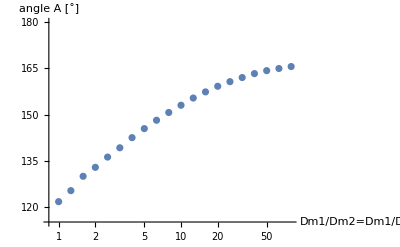

```mathematica
ListLogLinearPlot[{#[[1]],180/Pi*#[[2]]}&/@angleList,PlotRange->{115,180},AxesLabel->{"Dm1/Dm2=Dm1/Dm3", "angle A [˚]"}]
```

#### fitList

```mathematica
(*angleList={{1,2.1228466645782182,{xJunc->{0.027594019999884905,-0.00015311711294726147},dInt->0.04429347596302958,R->10000.,phiCircleB->3.6509656480955806,phiLin->-0.013890533636914998}},{1.2589,2.185468209774884,{xJunc->{-0.139751158136602,0.002047837701375237},dInt->0.0441102722435532,R->434.05329655438345,phiCircleB->3.6196548754972477,phiLin->-0.014288624225943564}},{1.5849,2.267065507878389,{xJunc->{-0.34807247574523986,0.007170721945022246},dInt->0.044436461801597806,R->315.74611435140395,phiCircleB->3.5788562264454953,phiLin->-0.025342722602590295}},{1.9953,2.317936921101449,{xJunc->{-0.5555202938073317,0.008069087584347857},dInt->0.043887387668202466,R->192.99507861737263,phiCircleB->3.5534205198339652,phiLin->-0.014913684914376677}},{2.5119,2.3762244740685565,{xJunc->{-0.7158591864292014,0.013494951798460214},dInt->0.043577122100101964,R->155.02199495115508,phiCircleB->3.5242767433504114,phiLin->-0.017259895577348666}},{3.1623,2.429079081983203,{xJunc->{-0.883174415783821,0.013246132888031989},dInt->0.043688436410800724,R->126.21684383634147,phiCircleB->3.497849439393088,phiLin->-0.014790639691111572}},{3.9811,2.486754810190323,{xJunc->{-1.041409649846175,0.015579603592256686},dInt->0.0435376833580208,R->104.41129675728946,phiCircleB->3.469011575289528,phiLin->-0.014721098004512335}},{5.0119,2.5380829572194106,{xJunc->{-1.1770535628454344,0.018201080868595076},dInt->0.04337622221236711,R->90.06453886350168,phiCircleB->3.4433475017749844,phiLin->-0.014912387339076178}},{6.3096,2.5855806974106343,{xJunc->{-1.3063255693790625,0.02038306653262506},dInt->0.043176474486894524,R->80.84528048747268,phiCircleB->3.4195986316793725,phiLin->-0.0150758496395184}},{7.9433,2.629718139814539,{xJunc->{-1.4324142544405631,0.021349051206961588},dInt->0.04297972812327249,R->73.70009101455547,phiCircleB->3.39752991047742,phiLin->-0.014437741556668923}},{10,2.6709554083559874,{xJunc->{-1.548299195067859,0.023154961837162976},dInt->0.0428049317646225,R->68.01863145527913,phiCircleB->3.376911276206696,phiLin->-0.014374526801535163}},{12.589,2.7119522407902688,{xJunc->{-1.6598625805138854,0.025773245327178857},dInt->0.04263564349010787,R->62.40436178130776,phiCircleB->3.3564128599895553,phiLin->-0.014765694295219121}},{15.849,2.746765580674415,{xJunc->{-1.7647315807819777,0.02766350922180303},dInt->0.04246613988411923,R->58.01489137102197,phiCircleB->3.339006190047482,phiLin->-0.014858075225068622}},{19.953,2.778764911758132,{xJunc->{-1.87653336110319,0.029342624333127412},dInt->0.04229053654953643,R->53.93685152005031,phiCircleB->3.3230065245056237,phiLin->-0.01481643186044432}},{25.119,2.805016739988842,{xJunc->{-1.997676057233804,0.031057630876090474},dInt->0.042133887725756276,R->50.34723208389854,phiCircleB->3.3098806103902687,phiLin->-0.014847604380351685}},{31.623,2.828370610639274,{xJunc->{-2.1509983736541325,0.03305682844186612},dInt->0.041969328103481564,R->46.34009514078484,phiCircleB->3.2982036750650527,phiLin->-0.014623618523342445}},{39.811,2.8506699415793406,{xJunc->{-2.3710388457812424,0.036758329208330824},dInt->0.0418630254120849,R->41.81111350512461,phiCircleB->3.2870540095950194,phiLin->-0.01474619167585154}},{50.119,2.867565089193877,{xJunc->{-2.7032698732668856,0.041730596775518596},dInt->0.04175014945502714,R->36.515028707101315,phiCircleB->3.278606435787751,phiLin->-0.014829875002391735}},{63.096,2.8798468726659845,{xJunc->{-3.272917950814822,0.05100944954463169},dInt->0.041620430822431026,R->30.04233272238111,phiCircleB->3.2724655440516974,phiLin->-0.014926144887599527}},{79.433,2.8908693315261234,{xJunc->{-4.419035693616477,0.06912970731284594},dInt->0.041496449080791004,R->21.719823354738438,phiCircleB->3.266954314621628,phiLin->-0.014978143018607903}}};*)
```

## Determine effective interfacial tensions σAB, σAC, σBC

Find points on the interfaces that are distant from the junction to measure the effective interfacial tensions.
Around this point, σ is determined by integrating the field dataσ over a rectangle crossing the interface. This integral is then divided by the width of the rectangle.

```mathematica
evalPointsS=evalPoints[#,15]&/@angleList;
```

Show the interface segments used to calculate σ

```mathematica
Manipulate[
Show[
ListDensityPlot[
Flatten[Transpose[{grid[[;;;;10,;;;;10,1]],grid[[;;;;10,;;;;10,2]],dataσ[[Floor@i,;;;;10,;;;;10]]},{3,1,2}],1],
PlotRange->All,
InterpolationOrder->0,
AspectRatio->1
],
Graphics[
Join[{Darker@Red,Thick},Flatten[{
Line[{{#[[1,1]],#[[1,2]]}-2#[[2]],{#[[1,1]],#[[1,2]]}+2#[[2]]}],
Line[{{#[[1,1]],#[[1,2]]}+2#[[2]]-1.5{-#[[2,2]],#[[2,1]]},{#[[1,1]],#[[1,2]]}+2#[[2]]+1.5{-#[[2,2]],#[[2,1]]}}],Line[{{#[[1,1]],#[[1,2]]}-2#[[2]]-1.5{-#[[2,2]],#[[2,1]]},{#[[1,1]],#[[1,2]]}-2#[[2]]+1.5{-#[[2,2]],#[[2,1]]}}]
}&/@evalPointsS[[Floor@i]],1]]
]
]
,{i,1,Length@angleList}]
```

```mathematica
σList=Table[
{angleList[[k,1]],
measureσ[angleList[[k]],dataσ[[k]],grid]
},{k,Length@angleList}];
```

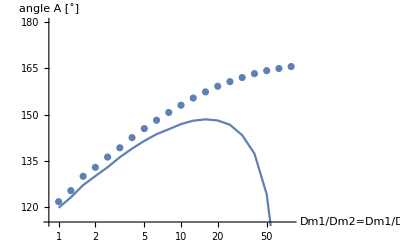

```mathematica
Show[
ListLogLinearPlot[{#[[1]],180/Pi*#[[2]]}&/@angleList,PlotRange->{115,180},AxesLabel->{"Dm1/Dm2=Dm1/Dm3", "angle A [˚]"}],
ListLogLinearPlot[{
({#[[1]],180/Pi*2ArcCos[Min[1,#[[2,2]]/#[[2,1]]/2]]})&/@σList
},
Joined->True]
]
```

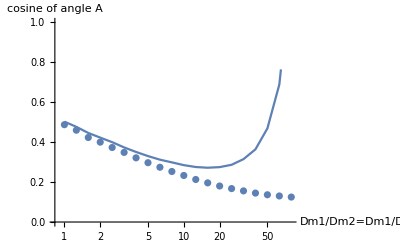

```mathematica
Show[
ListLogLinearPlot[{#[[1]],Cos[#[[2]]/2]}&/@angleList,PlotRange->{0,1},AxesLabel->{"Dm1/Dm2=Dm1/Dm3", "cosine of angle A"}],
ListLogLinearPlot[{
({#[[1]],#[[2,2]]/#[[2,1]]/2})&/@σList
},
Joined->True]
]
```

#### σList

```mathematica
(*σList={{1,{0.1382933423929382,0.1390766046584685}},{1.2589,{0.14603082247931104,0.1392778676680056}},{1.5849,{0.15478160443666958,0.13812609999284073}},{1.9953,{0.16484511946652516,0.13943443201109013}},{2.5119,{0.1755329295718236,0.14044380021137481}},{3.1623,{0.1869665931001121,0.1397631138571918}},{3.9811,{0.19932521124125577,0.13993346746680632}},{5.0119,{0.21188928687985106,0.13999995361586953}},{6.3096,{0.2241274363063676,0.14001392480347777}},{7.9433,{0.23571735564974522,0.14088767137655123}},{10,{0.24594356260777606,0.14017781171325344}},{12.589,{0.2532958266858071,0.13959333511285288}},{15.849,{0.2563264398795127,0.13943308298688925}},{19.953,{0.25305862853589955,0.13920100927170612}},{25.119,{0.24159344491710116,0.13853126597480392}},{31.623,{0.21969199522932756,0.13846149020651521}},{39.811,{0.1866799368704708,0.1359787393534799}},{50.119,{0.14330004207319305,0.13442860454762345}},{63.096,{0.09406391167265887,0.12961973953597392}},{79.433,{0.049156832936594605,0.12307047605331022}}};*)
```

## Core contribution T_core

To determine the x and y components of T_core, we need to integrate the field dataCoreTurnoverX & dataCoreTurnoverY over a triangle whose sides are perpendicular to the three interfaces.
If all interfaces are straight, the triangle can be arbitrarily large because the integrals over a single interface (far from the core region) vanishes.
As two interfaces are curved here, this is not the case and we need to substract the contribution that stems from the interfaces being curved (coreTurnoverCorr).

```mathematica
evalPointsCTS=evalPointsCT/@angleList;
```

```mathematica
Manipulate[
Show[
ListDensityPlot[
Flatten[Transpose[{gridCT[[;;;;100,;;;;100,1]],gridCT[[;;;;100,;;;;100,2]],dataCoreTurnoverX[[Floor@i,;;;;100,;;;;100]]},{3,1,2}],1],
PlotRange->All,
InterpolationOrder->0,
AspectRatio->1/2],
Graphics[Join[
{Darker@Red,Thick},
Circle[#[[1]],0.1]&/@evalPointsCTS[[Floor@i]],
Line[{#[[1]],#[[1]]+1#[[2]]}]&/@evalPointsCTS[[Floor@i]]]]
]
,{i,1,Length@angleList}]
```

```mathematica
coreTurnover={};
Monitor[Do[
Block[{ct},
ct=measureCT[angleList[[k]],{dataCoreTurnoverX[[k]],dataCoreTurnoverY[[k]]},gridCT];
Print[ct];
AppendTo[coreTurnover,ct];
],{k,Length@angleList}];,k]
```

{1,{-0.000613763,-0.00177649}}

{1.2589,{-0.00439023,0.00287136}}

{1.5849,{-0.00555898,0.00179439}}

{1.9953,{-0.00605572,0.000199471}}

{2.5119,{-0.00426881,-0.00244369}}

{3.1623,{-0.0042996,-0.00226285}}

{3.9811,{-0.00729368,-0.00276356}}

{5.0119,{-0.010725,-0.00515815}}

{6.3096,{-0.0121255,-0.00364526}}

{7.9433,{-0.0109657,-0.00406031}}

{10,{-0.00719258,-0.0044187}}

{12.589,{-0.00701273,-0.000613845}}

{15.849,{-0.00146052,-0.000295433}}

{19.953,{0.00384502,-0.00363805}}

{25.119,{0.013313,-0.0033766}}

{31.623,{0.0264361,-0.00268128}}

{39.811,{0.0409157,-0.00252216}}

{50.119,{0.0588819,-0.00169649}}

{63.096,{0.0787869,-0.00205468}}

{79.433,{0.0931321,-0.00105987}}

Angle prediction without correcting for interface curvature:

```mathematica
junctionAnglesPred=Table[
Block[{
thetaAB0=phiCircleB-Pi/2/.angleList[[k,3]],
thetaAC0=-phiCircleB+Pi/2+2phiLin/.angleList[[k,3]],
thetaBC=phiLin/.angleList[[k,3]]
},
{angleList[[k,1]],
{θAC,thetaBC,θAB}/.FindRoot[({Cos[thetaBC],Sin[thetaBC]}σList[[k,2,2]])
+({Cos[θAB],Sin[θAB]}σList[[k,2,1]])
+({Cos[θAC],Sin[θAC]}σList[[k,2,1]])
==coreTurnover[[k,2]],{{θAB,thetaAB0,0,Pi+thetaBC},{θAC,thetaAC0,-Pi+thetaBC,0}}]
}],{k,Length@angleList}]
```

{{1,{-2.10129,-0.0138905,2.09907}},{1.2589,{-2.11917,-0.0142886,2.05152}},{1.5849,{-2.09051,-0.0253427,2.01683}},{1.9953,{-2.04351,-0.0149137,2.01218}},{2.5119,{-1.99547,-0.0172599,1.99575}},{3.1623,{-1.96489,-0.0147906,1.9676}},{3.9811,{-1.94425,-0.0147211,1.95381}},{5.0119,{-1.9141,-0.0149124,1.95484}},{6.3096,{-1.90697,-0.0150758,1.92715}},{7.9433,{-1.88541,-0.0144377,1.91209}},{10,{-1.85877,-0.0143745,1.89139}},{12.589,{-1.87425,-0.0147657,1.8545}},{15.849,{-1.86181,-0.0148581,1.8366}},{19.953,{-1.82988,-0.0148164,1.85316}},{25.119,{-1.82238,-0.0148476,1.84346}},{31.623,{-1.82271,-0.0146236,1.83443}},{39.811,{-1.82277,-0.0147462,1.83365}},{50.119,{-1.84143,-0.0148299,1.83356}},{63.096,{-1.84196,-0.0149261,1.84668}},{79.433,{-1.90637,-0.0149781,1.85402}}}

```mathematica
angleAPred={#[[1]],(Max[Join[#,{360-Total@#}]]&@(180/Pi*Differences[#[[2]]]))}&/@junctionAnglesPred
```

{{1,121.064},{1.2589,121.037},{1.5849,124.667},{1.9953,127.626},{2.5119,131.32},{3.1623,134.685},{3.9811,136.658},{5.0119,138.327},{6.3096,140.321},{7.9433,142.419},{10,145.131},{12.589,146.358},{15.849,148.097},{19.953,148.977},{25.119,149.963},{31.623,150.461},{39.811,150.503},{50.119,149.439},{63.096,148.656},{79.433,144.546}}

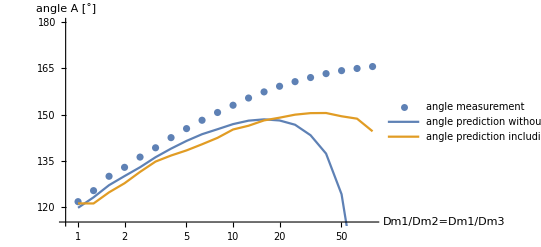

```mathematica
Show[
ListLogLinearPlot[{#[[1]],180/Pi*#[[2]]}&/@angleList,PlotRange->{115,180},AxesLabel->{"Dm1/Dm2=Dm1/Dm3", "angle A [˚]"},PlotLegends->{"angle measurement"}],
ListLogLinearPlot[{
({#[[1]],180/Pi*2ArcCos[Min[1,#[[2,2]]/#[[2,1]]/2]]})&/@σList,
angleAPred
},
Joined->True,
PlotLegends->{"angle prediction without core contribution","angle prediction including core contribution (without curvature correction)"}]
]
```

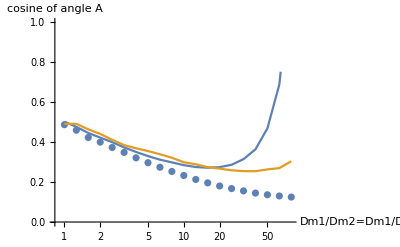

```mathematica
Show[
ListLogLinearPlot[{#[[1]],Cos[#[[2]]/2]}&/@angleList,PlotRange->{0,1},AxesLabel->{"Dm1/Dm2=Dm1/Dm3", "cosine of angle A"}],
ListLogLinearPlot[{
({#[[1]],#[[2,2]]/#[[2,1]]/2})&/@σList,
{#[[1]],Cos[Pi/180#[[2]]/2]}&/@angleAPred
},
Joined->True]
]
```

#### Core turnover list

```mathematica
(*coreTurnover={{1,{-0.0006137631284990776,-0.0017764922853390189}},{1.2589,{-0.004390229266050639,0.0028713563896997467}},{1.5849,{-0.005558976521135899,0.001794385154195349}},{1.9953,{-0.006055718667617879,0.00019947053381426356}},{2.5119,{-0.004268810749694244,-0.0024436924170946808}},{3.1623,{-0.0042996012022996554,-0.0022628500519134634}},{3.9811,{-0.007293677173644149,-0.0027635648621873316}},{5.0119,{-0.010725030440914588,-0.005158145950194897}},{6.3096,{-0.012125529928139542,-0.0036452567669556205}},{7.9433,{-0.010965738804412878,-0.004060308790359883}},{10,{-0.0071925818265885805,-0.0044187003430436736}},{12.589,{-0.007012730010687868,-0.0006138446147384558}},{15.849,{-0.0014605243327805643,-0.0002954328659122453}},{19.953,{0.00384502487544963,-0.003638048485286391}},{25.119,{0.013313028635065048,-0.003376603536216463}},{31.623,{0.026436128720199032,-0.002681284613322461}},{39.811,{0.040915701428084414,-0.002522157114851204}},{50.119,{0.0588818881068973,-0.00169648953659724}},{63.096,{0.07878687102195078,-0.0020546834659769106}},{79.433,{0.09313214965872657,-0.0010598700081001556}}};*)
```

### Correction to core turnover due to curved interfaces

Calculate turnover integral over the curved interface at a distance from the junction, rotate the turnover vector such that that interface piece alines with its contribution in the core-turnover integral and substrate this correction vector from the above calculated turnover vector.

```mathematica
evalPointsCTCorrS=Table[
evalPointsCTCorr[junction,{-9,4},"measArclength"->2],
{junction,angleList}];
```

```mathematica
Manipulate[
Show[
ListDensityPlot[
Flatten[Transpose[{gridCT[[;;;;50,;;;;50,1]],gridCT[[;;;;50,;;;;50,2]],dataCoreTurnoverX[[Floor@i,;;;;50,;;;;50]]},{3,1,2}],1],
PlotRange->All,
InterpolationOrder->0,
AspectRatio->10/15],
Graphics[Join[
{Darker@Red,Thick},
Circle[#[[1]],0.1]&/@evalPointsCTCorrS[[Floor@i,;;-2]],
Line[{#[[1]],#[[1]]+1#[[2]]}]&/@evalPointsCTCorrS[[Floor@i,;;-2]],
Line[{#[[1]]-2 {-#[[2,2]],#[[2,1]]},#[[1]]+2 {-#[[2,2]],#[[2,1]]}}]&/@evalPointsCTCorrS[[Floor@i,;;-2]],
Line[{#[[1]]-2{-#[[2,2]],#[[2,1]]},#[[1]]-2 {-#[[2,2]],#[[2,1]]}+2#[[2]]}]&/@evalPointsCTCorrS[[Floor@i,{1,3}]],
Line[{#[[1]]+2{-#[[2,2]],#[[2,1]]},#[[1]]+2{-#[[2,2]],#[[2,1]]}+2#[[2]]}]&/@evalPointsCTCorrS[[Floor@i,{1,3}]]
]]
]
,{i,1,Length@angleList}]
```

We need to determine the correction term on a smaller stretch of the interface as the interfaces are too short to measure the full stretch at a certain distance away from the junction.

```mathematica
coreTurnoverCorr={};
Monitor[Do[
Block[{
corr
},
corr=measureCTCorr[angleList[[k]],{dataCoreTurnoverX[[k]],dataCoreTurnoverY[[k]]},gridCT,"halfStretch"->True,"measurementWidth"->2];
Print[corr];
AppendTo[coreTurnoverCorr,corr];
],{k,1,Length@angleList}];,k]
```

{1,{0.000206522,0.000723751}}

{1.2589,{-0.00400971,0.0010256}}

{1.5849,{-0.00798143,0.00224628}}

{1.9953,{-0.006178,0.00109705}}

{2.5119,{-0.00730106,-0.000263351}}

{3.1623,{-0.0103958,0.000420005}}

{3.9811,{-0.0150086,0.000980327}}

{5.0119,{-0.0186879,0.00112516}}

{6.3096,{-0.0255144,-0.000166024}}

{7.9433,{-0.0276051,0.00112263}}

{10,{-0.03014,0.000556562}}

{12.589,{-0.0328492,-0.000153585}}

{15.849,{-0.0339266,-0.000091064}}

{19.953,{-0.0368996,-0.000377318}}

{25.119,{-0.036835,0.000246362}}

{31.623,{-0.0351078,0.00018132}}

{39.811,{-0.0301839,0.000590916}}

{50.119,{-0.026129,0.000174377}}

{63.096,{-0.0200381,0.0002956}}

{79.433,{-0.0155062,0.000261381}}

```mathematica
junctionAnglesPredCorr=Table[
Block[{
thetaAB0=phiCircleB-Pi/2/.angleList[[k,3]],
thetaAC0=-phiCircleB+Pi/2+2phiLin/.angleList[[k,3]],
thetaBC=phiLin/.angleList[[k,3]]
},
{angleList[[k,1]],
{θAC,thetaBC,θAB}/.FindRoot[({Cos[thetaBC],Sin[thetaBC]}σList[[k,2,2]])
+({Cos[θAB],Sin[θAB]}σList[[k,2,1]])
+({Cos[θAC],Sin[θAC]}σList[[k,2,1]])
==coreTurnover[[k,2]]-coreTurnoverCorr[[k,2]],{{θAB,thetaAB0,0,Pi+thetaBC},{θAC,thetaAC0,-Pi+thetaBC,0}}]
}],{k,Length@angleList}]
```

{{1,{-2.09699,-0.0138905,2.10512}},{1.2589,{-2.09699,-0.0142886,2.04207}},{1.5849,{-2.04701,-0.0253427,2.00208}},{1.9953,{-2.01551,-0.0149137,1.99854}},{2.5119,{-1.97467,-0.0172599,1.97113}},{3.1623,{-1.9317,-0.0147906,1.94091}},{3.9811,{-1.89612,-0.0147211,1.92159}},{5.0119,{-1.856,-0.0149124,1.91954}},{6.3096,{-1.84635,-0.0150758,1.86797}},{7.9433,{-1.81221,-0.0144377,1.8629}},{10,{-1.78624,-0.0143745,1.83674}},{12.589,{-1.81135,-0.0147657,1.7832}},{15.849,{-1.79845,-0.0148581,1.76354}},{19.953,{-1.75439,-0.0148164,1.77873}},{25.119,{-1.73702,-0.0148476,1.77247}},{31.623,{-1.73584,-0.0146236,1.75763}},{39.811,{-1.72836,-0.0147462,1.76252}},{50.119,{-1.74652,-0.0148299,1.74156}},{63.096,{-1.72166,-0.0149261,1.74867}},{79.433,{-1.75427,-0.0149781,1.68189}}}

```mathematica
angleAPredCorr={#[[1]],(Max[Join[#,{360-Total@#}]]&@(180/Pi*Differences[#[[2]]]))}&/@junctionAnglesPredCorr
```

{{1,121.41},{1.2589,122.849},{1.5849,128.004},{1.9953,130.012},{2.5119,133.923},{3.1623,138.116},{3.9811,141.262},{5.0119,143.678},{6.3096,147.185},{7.9433,149.432},{10,152.419},{12.589,154.048},{15.849,155.913},{19.953,157.567},{25.119,158.921},{31.623,159.839},{39.811,159.987},{50.119,160.148},{63.096,161.165},{79.433,163.122}}

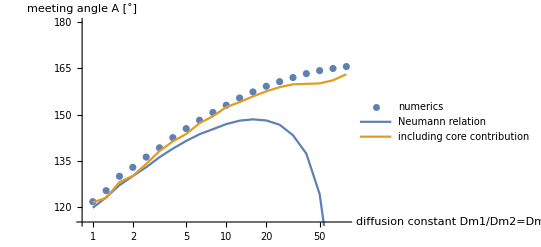

```mathematica
Show[
ListLogLinearPlot[{#[[1]],180/Pi*#[[2]]}&/@angleList,PlotRange->{115,180},AxesLabel->{"diffusion constant Dm1/Dm2=Dm1/Dm3","meeting angle A [˚]"},PlotLegends->{"numerics"}],
ListLogLinearPlot[{
({#[[1]],180/Pi*2ArcCos[Min[1,#[[2,2]]/#[[2,1]]/2]]})&/@σList,
angleAPredCorr
},
Joined->True,
PlotLegends->{"Neumann relation", "including core contribution"}]
]
```

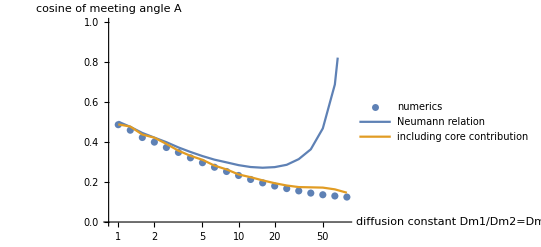

```mathematica
Show[
ListLogLinearPlot[{#[[1]],Cos[#[[2]]/2]}&/@angleList,PlotRange->{0,1},AxesLabel->{"diffusion constant Dm1/Dm2=Dm1/Dm3","cosine of meeting angle A"},PlotLegends->{"numerics"}],
ListLogLinearPlot[{
({#[[1]],#[[2,2]]/#[[2,1]]/2})&/@σList,
{#[[1]],Cos[Pi/180#[[2]]/2]}&/@angleAPredCorr
},
Joined->True,
PlotLegends->{"Neumann relation", "including core contribution"}]
]
```

#### Correction list

```mathematica
(*coreTurnoverCorr={{1,{0.00020652152825589138,0.0007237510845880799}},{1.2589,{-0.00400971417858723,0.0010256043198147765}},{1.5849,{-0.007981425696564523,0.002246282466723078}},{1.9953,{-0.006178004270203777,0.0010970520205746451}},{2.5119,{-0.007301060151423611,-0.0002633514796448969}},{3.1623,{-0.010395824683800677,0.0004200054704279542}},{3.9811,{-0.015008586362798965,0.0009803270026950922}},{5.0119,{-0.018687870573012966,0.0011251577151213637}},{6.3096,{-0.02551444974919933,-0.00016602424579122014}},{7.9433,{-0.027605073339679854,0.0011226266915021297}},{10,{-0.030140012397964776,0.0005565617397089613}},{12.589,{-0.032849231906553686,-0.00015358465974842604}},{15.849,{-0.033926574991317966,-0.00009106400088445838}},{19.953,{-0.036899604862661375,-0.0003773182251293394}},{25.119,{-0.03683500045311368,0.0002463620425357323}},{31.623,{-0.03510783081682618,0.00018132027748387443}},{39.811,{-0.03018388654172563,0.0005909160422606342}},{50.119,{-0.026129027445041288,0.00017437686957928787}},{63.096,{-0.020038113166863627,0.0002955995035705311}},{79.433,{-0.015506177467386327,0.00026138108386393444}}};*)
```